```mathematica
(*Needs["VectorAnalysis`"]
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];*)

k=0.0677/4;
{xMin,xMax}={-π/k,π/k};

TMax=5000;
(*uSol[t_,x_]=u[t,x]/.*)uSolpbc[t_,x_]=u[t,x]/.NDSolve[{D[u[t,x], t]==-100 D[(u[t,x]^3 D[u[t,x], x,x,x]), x]+1/3 D[(u[t,x]^3 D[u[t,x], x]), x]-5 D[((u[t,x]/(1+u[t,x]))^2 D[u[t,x], x]), x],u[0,x]==1-0.1 Cos[k*x],
u[t,xMin]== u[t,xMax],
Derivative[0,1]u[t,xMin]==Derivative[0,1]u[t,xMax],
Derivative[0,2]u[t,xMin]==Derivative[0,2]u[t,xMax],
Derivative[0,3]u[t,xMin]==Derivative[0,3]u[t,xMax]},
u,
{t,0,TMax},
{x,xMin,xMax},
(*PrecisionGoal->Automatic,*)
Method->{"LSODA","MaxDifferenceOrder"->12},


(*Method->{"MethodOfLines","Method"->"BDF","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->200,"DifferenceOrder"->5}}*)]⟦1⟧ // AbsoluteTiming
```

NDSolve::ndsz: At t == 3858.74, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: Scaled local spatial error estimate of 10635.4 at t = 3858.74 in the direction of independent variable x is much greater than prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

{0.084416,InterpolatingFunction[{{0.,3858.74},{-185.618,185.618}},<>][t,x]}

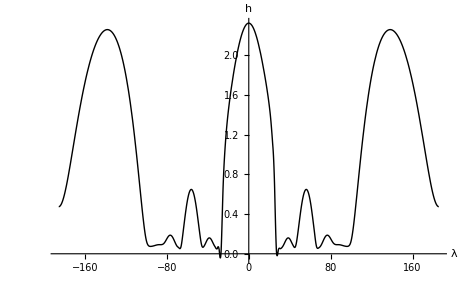

```mathematica
Plot[
uSolpbc[4711,x],{x,xMin,xMax},PlotStyle->{Black,Thick},
AxesLabel->{"λ","h"},
BaseStyle->{FontWeight->"Plain",FontSize->18}
]
```

```mathematica
p1=Plot[uSolpbc[0.1 TMax,x],{x,xMin,xMax},PlotStyle->Blue];
p2=Plot[uSolpbc[0.5 TMax,x],{x,xMin,xMax},PlotStyle->Blue];
p3=Plot[uSolpbc[0.8 TMax,x],{x,xMin,xMax},PlotStyle->Blue];
p4=Plot[uSolpbc[ TMax,x],{x,xMin,xMax},PlotStyle->Blue];
Show[p1,p2,p3, PlotRange->All,FrameLabel->{"x=λ","h(x,t)"},PlotLabel->"G=1,S=100,Pr=7.02,M=35.1,K=1,B=0",Frame->True,TextStyle->{FontFamily->"Helvetica",FontSize->12}]
```

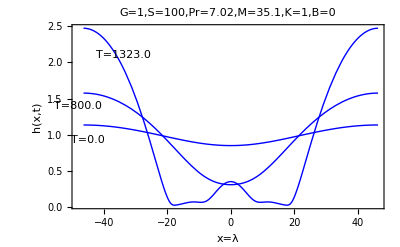

```mathematica
NIntegrate[uSolpbc[0.1 TMax,x],{x,xMin,xMax}]
NIntegrate[uSolpbc[0.5 TMax,x],{x,xMin,xMax}]
NIntegrate[uSolpbc[0.8 TMax,x],{x,xMin,xMax}]
NIntegrate[uSolpbc[ TMax,x],{x,xMin,xMax}]
```

92.8092

92.8079

92.808

92.8076

```mathematica
Manipulate[
Plot[uSolpbc[t,x], {x,xMin,xMax}, PlotRange->{{xMin,xMax},{0,2}},PlotStyle->Red],
{t,0,TMax,TMax/25}]
```